# Bootstrapping v4.0 (smh)

## I mean at some point I am bound to get this right

```mathematica
ModuleDirectory = NotebookDirectory[] <> "../modules/";
<< (ModuleDirectory<> "debugTools.wl");
<< (ModuleDirectory<> "dataLoader.wl");
<< (ModuleDirectory<> "bootstraptdl.wl");
<< (ModuleDirectory<> "defect.wl");
```

math4ti2: Mathematica interface to 4ti2 (http://www.4ti2.de/)
Copyright (C) 2017, Ralf Hemmecke <ralf@hemmecke.org>
Copyright (C) 2017, Silviu Radu <sradu@risc.jku.at>

```mathematica
?dataLoader`*
```

```mathematica
md = ModularDataFoldZ2FixedMinimal[] // Time;
mb = ModularBootstrapTraces[md] //Time;
traces = mb["defects"] // ToRoots//Time;
traces //Transpose // MatrixForm
```

Time:   0.069655

Time:   1.48738

Time:   0.257848

(1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | 2 √(5+√5) | 2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(2 (5+2 √5)) | 2 √(2 (5+2 √5))
1 | -1 | 1 | 1 | -1 | -√2 | √2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | -√(2 (5+√5)) | √(2 (5+√5)) | -√(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | 2 √(5+√5) | -2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(2 (5+2 √5)) | 2 √(2 (5+2 √5))
-2 | 0 | 2 | 0 | 0 | 0 | √2 | -√2 | √5 | -√5 | -1 | 1 | 0 | 0 | 0 | -√(3-√5) | -√(3+√5) | √(3+√5) | √(3-√5) | 0 | 0 | -2 | 2 | 0 | √2 | -√2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | -1 | -1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3+√5) | 1/2 (3-√5) | 1/2 (3-√5) | 0 | 0 | 0 | √(5-√5) | -√(5-√5) | -√(5-√5) | √(5-√5) | 0 | 0 | 0 | √(2 (5-2 √5)) | -√(2 (5-2 √5)) | -√(2 (5-2 √5)) | √(2 (5-2 √5)) | 0 | 0
1 | -1 | 1 | -1 | 1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3+√5) | 1/2 (3-√5) | 1/2 (3-√5) | 0 | 0 | 0 | -√(5-√5) | -√(5-√5) | √(5-√5) | √(5-√5) | 0 | 0 | 0 | √(2 (5-2 √5)) | -√(2 (5-2 √5)) | √(2 (5-2 √5)) | -√(2 (5-2 √5)) | 0 | 0
2 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | -4 | -√10 | √10 | √10 | -√10 | 0 | -2 | -2 | -2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 | 0 | 2 | 0 | 0 | 0 | -√2 | √2 | 0 | 0 | -1+√5 | 1-√5 | 0 | 0 | 0 | √(3-√5) | -√(3-√5) | √(3-√5) | -√(3-√5) | 0 | 0 | 3-√5 | -3+√5 | 0 | √(7-3 √5) | -√(7-3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | -√(7-3 √5) | -√(7-3 √5) | √(2 (5-√5)) | √(2 (5-√5)) | √(2 (5-√5)) | √(2 (5-√5)) | 3-√5 | -2 √(5-√5) | -2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(2 (5-2 √5)) | 2 √(2 (5-2 √5))
1 | -1 | 1 | 1 | -1 | √2 | -√2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | -√(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | -√(7-3 √5) | -√(7-3 √5) | -√(2 (5-√5)) | √(2 (5-√5)) | -√(2 (5-√5)) | √(2 (5-√5)) | 3-√5 | -2 √(5-√5) | 2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) |  |  | -2 √(2 (5-2 √5)) | 2 √(2 (5-2 √5))
-2 | 0 | 2 | 0 | 0 | 0 | √2 | -√2 | 0 | 0 | -1-√5 | 1+√5 | 0 | 0 | 0 | √(3+√5) | -√(3+√5) | √(3+√5) | -√(3+√5) | 0 | 0 | 3+√5 | -3-√5 | 0 | -√(7+3 √5) | √(7+3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 0 | 2 | -2 | 0 | 0 | 0 | 0 | -1 | -1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | -2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 | 0 | 2 | 0 | 0 | 0 | -√2 | √2 | -√5 | √5 | -1 | 1 | 0 | 0 | 0 | -√(3+√5) | -√(3-√5) | √(3-√5) | √(3+√5) | 0 | 0 | -2 | 2 | 0 | -√2 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 0 | 2 | 2 | 0 | 0 | 2 √2 | 2 √2 | 1 | 1 | 1 | 1 | 0 | 0 | 4 | √2 | √2 | √2 | √2 | 0 | -2 | -2 | -2 | 2 | -2 √2 | -2 √2 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 | 0 | 2 | 0 | 0 | 0 | √2 | -√2 | 0 | 0 | -1+√5 | 1-√5 | 0 | 0 | 0 | -√(3-√5) | √(3-√5) | -√(3-√5) | √(3-√5) | 0 | 0 | 3-√5 | -3+√5 | 0 | -√(7-3 √5) | √(7-3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 1-√5 | 1-√5 | 1-√5 | 1-√5 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 3-√5 | 3-√5 | 3-√5 | -2+2 √5 | 0 | 0 | 0 | 0 | 0 | 0 | -6+2 √5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | -1 | -1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3-√5) | 1/2 (3+√5) | 1/2 (3+√5) | 0 | 0 | 0 | √(5+√5) | -√(5+√5) | -√(5+√5) | √(5+√5) | 0 | 0 | 0 | -√(2 (5+2 √5)) | √(2 (5+2 √5)) | √(2 (5+2 √5)) | -√(2 (5+2 √5)) | 0 | 0
1 | -1 | 1 | -1 | 1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3-√5) | 1/2 (3+√5) | 1/2 (3+√5) | 0 | 0 | 0 | -√(5+√5) | -√(5+√5) | √(5+√5) | √(5+√5) | 0 | 0 | 0 | -√(2 (5+2 √5)) | √(2 (5+2 √5)) | -√(2 (5+2 √5)) | √(2 (5+2 √5)) | 0 | 0
-2 | 0 | 2 | 0 | 0 | 0 | √2 | -√2 | -√5 | √5 | -1 | 1 | 0 | 0 | 0 | √(3+√5) | √(3-√5) | -√(3-√5) | -√(3+√5) | 0 | 0 | -2 | 2 | 0 | √2 | -√2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | -1 | 1 | -1 | 1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3+√5) | 1/2 (3-√5) | 1/2 (3-√5) | 0 | 0 | 0 | √(5-√5) | √(5-√5) | -√(5-√5) | -√(5-√5) | 0 | 0 | 0 | -√(2 (5-2 √5)) | √(2 (5-2 √5)) | -√(2 (5-2 √5)) | √(2 (5-2 √5)) | 0 | 0
1 | 1 | 1 | -1 | -1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3+√5) | 1/2 (3-√5) | 1/2 (3-√5) | 0 | 0 | 0 | -√(5-√5) | √(5-√5) | √(5-√5) | -√(5-√5) | 0 | 0 | 0 | -√(2 (5-2 √5)) | √(2 (5-2 √5)) | √(2 (5-2 √5)) | -√(2 (5-2 √5)) | 0 | 0
1 | -1 | 1 | 1 | -1 | √2 | -√2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | -√(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | -√(7-3 √5) | -√(7-3 √5) | √(2 (5-√5)) | -√(2 (5-√5)) | √(2 (5-√5)) | -√(2 (5-√5)) | 3-√5 | 2 √(5-√5) | -2 √(5-√5) |  |  | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(2 (5-2 √5)) | -2 √(2 (5-2 √5))
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | -√(7-3 √5) | -√(7-3 √5) | -√(2 (5-√5)) | -√(2 (5-√5)) | -√(2 (5-√5)) | -√(2 (5-√5)) | 3-√5 | 2 √(5-√5) | 2 √(5-√5) |  |  |  |  | -2 √(2 (5-2 √5)) | -2 √(2 (5-2 √5))
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | -√(3-√5) | -√(3-√5) | -√(3-√5) | -√(3-√5) | -√(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | √(2 (5-√5)) | √(2 (5-√5)) | √(2 (5-√5)) | √(2 (5-√5)) | 3-√5 | 2 √(5-√5) | 2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(2 (5-2 √5)) | -2 √(2 (5-2 √5))
1 | -1 | 1 | 1 | -1 | -√2 | √2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 2 | -√(3-√5) | -√(3-√5) | -√(3-√5) | -√(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | -√(2 (5-√5)) | √(2 (5-√5)) | -√(2 (5-√5)) | √(2 (5-√5)) | 3-√5 | 2 √(5-√5) | -2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) |  |  | 2 √(2 (5-2 √5)) | -2 √(2 (5-2 √5))
2 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 1+√5 | 1+√5 | 1+√5 | 1+√5 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 3+√5 | 3+√5 | 3+√5 | -2-2 √5 | 0 | 0 | 0 | 0 | 0 | 0 | -6-2 √5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 | 0 | 2 | 0 | 0 | 0 | -√2 | √2 | √5 | -√5 | -1 | 1 | 0 | 0 | 0 | √(3-√5) | √(3+√5) | -√(3+√5) | -√(3-√5) | 0 | 0 | -2 | 2 | 0 | -√2 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 0 | 2 | 2 | 0 | 0 | -2 √2 | -2 √2 | 1 | 1 | 1 | 1 | 0 | 0 | 4 | -√2 | -√2 | -√2 | -√2 | 0 | -2 | -2 | -2 | 2 | 2 √2 | 2 √2 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | -1 | 1 | -1 | 1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3-√5) | 1/2 (3+√5) | 1/2 (3+√5) | 0 | 0 | 0 | √(5+√5) | √(5+√5) | -√(5+√5) | -√(5+√5) | 0 | 0 | 0 | √(2 (5+2 √5)) | -√(2 (5+2 √5)) | √(2 (5+2 √5)) | -√(2 (5+2 √5)) | 0 | 0
1 | 1 | 1 | -1 | -1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3-√5) | 1/2 (3+√5) | 1/2 (3+√5) | 0 | 0 | 0 | -√(5+√5) | √(5+√5) | √(5+√5) | -√(5+√5) | 0 | 0 | 0 | √(2 (5+2 √5)) | -√(2 (5+2 √5)) | -√(2 (5+2 √5)) | √(2 (5+2 √5)) | 0 | 0
-2 | 0 | 2 | 0 | 0 | 0 | -√2 | √2 | 0 | 0 | -1-√5 | 1+√5 | 0 | 0 | 0 | -√(3+√5) | √(3+√5) | -√(3+√5) | √(3+√5) | 0 | 0 | 3+√5 | -3-√5 | 0 | √(7+3 √5) | -√(7+3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | -1 | 1 | 1 | -1 | -√2 | √2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | √(2 (5+√5)) | -√(2 (5+√5)) | √(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | -2 √(5+√5) | 2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(2 (5+2 √5)) | -2 √(2 (5+2 √5))
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | -2 √(5+√5) | -2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(2 (5+2 √5)) | -2 √(2 (5+2 √5))
2 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | -4 | √10 | -√10 | -√10 | √10 | 0 | -2 | -2 | -2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | -1 | 1 | 1 | -1 | -√2 | √2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 2 | -√(3-√5) | -√(3-√5) | -√(3-√5) | -√(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | √(2 (5-√5)) | -√(2 (5-√5)) | √(2 (5-√5)) | -√(2 (5-√5)) | 3-√5 | -2 √(5-√5) | 2 √(5-√5) |  |  | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(2 (5-2 √5)) | 2 √(2 (5-2 √5))
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | -√(3-√5) | -√(3-√5) | -√(3-√5) | -√(3-√5) | -√(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | -√(2 (5-√5)) | -√(2 (5-√5)) | -√(2 (5-√5)) | -√(2 (5-√5)) | 3-√5 | -2 √(5-√5) | -2 √(5-√5) |  |  |  |  | 2 √(2 (5-2 √5)) | 2 √(2 (5-2 √5))
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | -2 √(5+√5) | -2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(2 (5+2 √5)) | -2 √(2 (5+2 √5))
1 | -1 | 1 | 1 | -1 | √2 | -√2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | -√(2 (5+√5)) | √(2 (5+√5)) | -√(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | -2 √(5+√5) | 2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(2 (5+2 √5)) | -2 √(2 (5+2 √5))
1 | -1 | 1 | 1 | -1 | √2 | -√2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | √(2 (5+√5)) | -√(2 (5+√5)) | √(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | 2 √(5+√5) | -2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(2 (5+2 √5)) | 2 √(2 (5+2 √5))
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | 2 √(5+√5) | 2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(2 (5+2 √5)) | 2 √(2 (5+2 √5)))

```mathematica
d=md["S"][[1,1]]^(-2)//FullSimplify // Echo;
r=Total@Flatten[md["Z"]^2]  // Echo;
```

160 (3+√5)

84

```mathematica
potts=ModularDataMinimal[6,5, "D"];
s=potts["S"];
z =potts["Z"];
z//Flatten//Total//Echo;
```

12

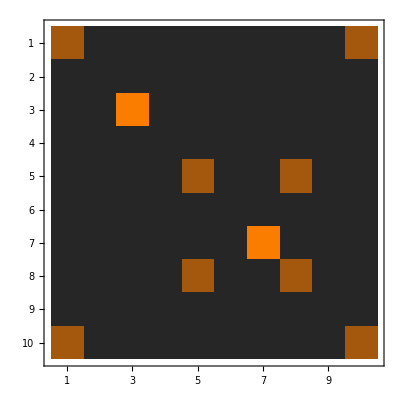

```mathematica
z//MatrixPlot
```

```mathematica
s//Simplify//MatrixForm
```

(1/2 √(1/30 (5-√5)) | 1/2 √(1/10 (5+√5)) | √(1/30 (5+√5)) | √(1/8-1/(8 √5)) | 1/2 √(1/30 (5+√5)) | 1/2 √(1/10 (5+√5)) | √(1/30 (5-√5)) | 1/2 √(1/30 (5+√5)) | √(1/8-1/(8 √5)) | 1/2 √(1/30 (5-√5))
1/2 √(1/10 (5+√5)) | √(1/8-1/(8 √5)) | 0 | 1/2 √(1/10 (5+√5)) | √(1/8-1/(8 √5)) | -1/2 √(1/10 (5-√5)) | 0 | -1/2 √(1/10 (5-√5)) | -1/2 √(1/10 (5+√5)) | -1/2 √(1/10 (5+√5))
√(1/30 (5+√5)) | 0 | √(1/30 (5-√5)) | 0 | -√(1/30 (5-√5)) | 0 | -√(1/30 (5+√5)) | -√(1/30 (5-√5)) | 0 | √(1/30 (5+√5))
√(1/8-1/(8 √5)) | 1/2 √(1/10 (5+√5)) | 0 | -1/2 √(1/10 (5-√5)) | -1/2 √(1/10 (5+√5)) | -1/2 √(1/10 (5+√5)) | 0 | 1/2 √(1/10 (5+√5)) | √(1/8-1/(8 √5)) | -1/2 √(1/10 (5-√5))
1/2 √(1/30 (5+√5)) | √(1/8-1/(8 √5)) | -√(1/30 (5-√5)) | -1/2 √(1/10 (5+√5)) | -1/2 √(1/30 (5-√5)) | √(1/8-1/(8 √5)) | √(1/30 (5+√5)) | -1/2 √(1/30 (5-√5)) | -1/2 √(1/10 (5+√5)) | 1/2 √(1/30 (5+√5))
1/2 √(1/10 (5+√5)) | -1/2 √(1/10 (5-√5)) | 0 | -1/2 √(1/10 (5+√5)) | √(1/8-1/(8 √5)) | √(1/8-1/(8 √5)) | 0 | -1/2 √(1/10 (5-√5)) | 1/2 √(1/10 (5+√5)) | -1/2 √(1/10 (5+√5))
√(1/30 (5-√5)) | 0 | -√(1/30 (5+√5)) | 0 | √(1/30 (5+√5)) | 0 | -√(1/30 (5-√5)) | √(1/30 (5+√5)) | 0 | √(1/30 (5-√5))
1/2 √(1/30 (5+√5)) | -1/2 √(1/10 (5-√5)) | -√(1/30 (5-√5)) | 1/2 √(1/10 (5+√5)) | -1/2 √(1/30 (5-√5)) | -1/2 √(1/10 (5-√5)) | √(1/30 (5+√5)) | -1/2 √(1/30 (5-√5)) | 1/2 √(1/10 (5+√5)) | 1/2 √(1/30 (5+√5))
√(1/8-1/(8 √5)) | -1/2 √(1/10 (5+√5)) | 0 | √(1/8-1/(8 √5)) | -1/2 √(1/10 (5+√5)) | 1/2 √(1/10 (5+√5)) | 0 | 1/2 √(1/10 (5+√5)) | -1/2 √(1/10 (5-√5)) | -1/2 √(1/10 (5-√5))
1/2 √(1/30 (5-√5)) | -1/2 √(1/10 (5+√5)) | √(1/30 (5+√5)) | -1/2 √(1/10 (5-√5)) | 1/2 √(1/30 (5+√5)) | -1/2 √(1/10 (5+√5)) | √(1/30 (5-√5)) | 1/2 √(1/30 (5+√5)) | -1/2 √(1/10 (5-√5)) | 1/2 √(1/30 (5-√5)))

```mathematica
s.z.s//Simplify //MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
k=z//Flatten//Total; 
n=First@Dimensions@z;
p=Array[x,{k,n}];
FindInstance[Thread[Flatten[Transpose[p]. p] == Flatten[z]],p//Flatten,Complexes]
```

$Aborted

```mathematica
posQ[r_]:=With[{nz=DeleteCases[r,0]},nz=!={}&&First[nz]>0];

integerGram[z_]:=Module[{n=Length[z],zero,cand,go},If[z=!=Transpose[z]||Min[Eigenvalues[N@z]]<-10.^-8,Return[$Failed]];
zero=ConstantArray[0,{n,n}];
cand=Select[Tuples[Range[-#,#]&/@Floor[Sqrt[Diagonal[z]]]],posQ];
go[m_,i_,acc_]:=If[m===zero,Throw[acc],If[Min[Diagonal[m]]>=0&&Min[Eigenvalues[N@m]]>-10.^-8,Do[With[{r=cand[[j]]},If[And@@Thread[r^2<=Diagonal[m]],go[m-Outer[Times,r,r],j,Append[acc,r]]]],{j,i,Length[cand]}]]];
Catch[go[z,1,{}];$Failed]];
n=integerGram[z];
n//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
z//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Transpose[n] . n //MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
k=n //Dimensions//First
```

6

```mathematica
S=Array[x,{k,k}];
FindInstance[
Join[{
Thread[Flatten[ConjugateTranspose[S]. S] == Flatten[IdentityMatrix[k]]],
Thread[Flatten[Transpose[n]. S . n] == Flatten[s]]
}]
,S//Flatten,Complexes]
```

{}

```mathematica
Join[{
Thread[Flatten[ConjugateTranspose[S]. S] == Flatten[IdentityMatrix[k]]],
Thread[Flatten[Transpose[n]. S . n] == Flatten[s]]
}]
```

{{Conjugate[x[1,1]] x[1,1]+Conjugate[x[2,1]] x[2,1]+Conjugate[x[3,1]] x[3,1]+Conjugate[x[4,1]] x[4,1]+Conjugate[x[5,1]] x[5,1]+Conjugate[x[6,1]] x[6,1]==1,Conjugate[x[1,1]] x[1,2]+Conjugate[x[2,1]] x[2,2]+Conjugate[x[3,1]] x[3,2]+Conjugate[x[4,1]] x[4,2]+Conjugate[x[5,1]] x[5,2]+Conjugate[x[6,1]] x[6,2]==0,Conjugate[x[1,1]] x[1,3]+Conjugate[x[2,1]] x[2,3]+Conjugate[x[3,1]] x[3,3]+Conjugate[x[4,1]] x[4,3]+Conjugate[x[5,1]] x[5,3]+Conjugate[x[6,1]] x[6,3]==0,Conjugate[x[1,1]] x[1,4]+Conjugate[x[2,1]] x[2,4]+Conjugate[x[3,1]] x[3,4]+Conjugate[x[4,1]] x[4,4]+Conjugate[x[5,1]] x[5,4]+Conjugate[x[6,1]] x[6,4]==0,Conjugate[x[1,1]] x[1,5]+Conjugate[x[2,1]] x[2,5]+Conjugate[x[3,1]] x[3,5]+Conjugate[x[4,1]] x[4,5]+Conjugate[x[5,1]] x[5,5]+Conjugate[x[6,1]] x[6,5]==0,Conjugate[x[1,1]] x[1,6]+Conjugate[x[2,1]] x[2,6]+Conjugate[x[3,1]] x[3,6]+Conjugate[x[4,1]] x[4,6]+Conjugate[x[5,1]] x[5,6]+Conjugate[x[6,1]] x[6,6]==0,Conjugate[x[1,2]] x[1,1]+Conjugate[x[2,2]] x[2,1]+Conjugate[x[3,2]] x[3,1]+Conjugate[x[4,2]] x[4,1]+Conjugate[x[5,2]] x[5,1]+Conjugate[x[6,2]] x[6,1]==0,Conjugate[x[1,2]] x[1,2]+Conjugate[x[2,2]] x[2,2]+Conjugate[x[3,2]] x[3,2]+Conjugate[x[4,2]] x[4,2]+Conjugate[x[5,2]] x[5,2]+Conjugate[x[6,2]] x[6,2]==1,Conjugate[x[1,2]] x[1,3]+Conjugate[x[2,2]] x[2,3]+Conjugate[x[3,2]] x[3,3]+Conjugate[x[4,2]] x[4,3]+Conjugate[x[5,2]] x[5,3]+Conjugate[x[6,2]] x[6,3]==0,Conjugate[x[1,2]] x[1,4]+Conjugate[x[2,2]] x[2,4]+Conjugate[x[3,2]] x[3,4]+Conjugate[x[4,2]] x[4,4]+Conjugate[x[5,2]] x[5,4]+Conjugate[x[6,2]] x[6,4]==0,Conjugate[x[1,2]] x[1,5]+Conjugate[x[2,2]] x[2,5]+Conjugate[x[3,2]] x[3,5]+Conjugate[x[4,2]] x[4,5]+Conjugate[x[5,2]] x[5,5]+Conjugate[x[6,2]] x[6,5]==0,Conjugate[x[1,2]] x[1,6]+Conjugate[x[2,2]] x[2,6]+Conjugate[x[3,2]] x[3,6]+Conjugate[x[4,2]] x[4,6]+Conjugate[x[5,2]] x[5,6]+Conjugate[x[6,2]] x[6,6]==0,Conjugate[x[1,3]] x[1,1]+Conjugate[x[2,3]] x[2,1]+Conjugate[x[3,3]] x[3,1]+Conjugate[x[4,3]] x[4,1]+Conjugate[x[5,3]] x[5,1]+Conjugate[x[6,3]] x[6,1]==0,Conjugate[x[1,3]] x[1,2]+Conjugate[x[2,3]] x[2,2]+Conjugate[x[3,3]] x[3,2]+Conjugate[x[4,3]] x[4,2]+Conjugate[x[5,3]] x[5,2]+Conjugate[x[6,3]] x[6,2]==0,Conjugate[x[1,3]] x[1,3]+Conjugate[x[2,3]] x[2,3]+Conjugate[x[3,3]] x[3,3]+Conjugate[x[4,3]] x[4,3]+Conjugate[x[5,3]] x[5,3]+Conjugate[x[6,3]] x[6,3]==1,Conjugate[x[1,3]] x[1,4]+Conjugate[x[2,3]] x[2,4]+Conjugate[x[3,3]] x[3,4]+Conjugate[x[4,3]] x[4,4]+Conjugate[x[5,3]] x[5,4]+Conjugate[x[6,3]] x[6,4]==0,Conjugate[x[1,3]] x[1,5]+Conjugate[x[2,3]] x[2,5]+Conjugate[x[3,3]] x[3,5]+Conjugate[x[4,3]] x[4,5]+Conjugate[x[5,3]] x[5,5]+Conjugate[x[6,3]] x[6,5]==0,Conjugate[x[1,3]] x[1,6]+Conjugate[x[2,3]] x[2,6]+Conjugate[x[3,3]] x[3,6]+Conjugate[x[4,3]] x[4,6]+Conjugate[x[5,3]] x[5,6]+Conjugate[x[6,3]] x[6,6]==0,Conjugate[x[1,4]] x[1,1]+Conjugate[x[2,4]] x[2,1]+Conjugate[x[3,4]] x[3,1]+Conjugate[x[4,4]] x[4,1]+Conjugate[x[5,4]] x[5,1]+Conjugate[x[6,4]] x[6,1]==0,Conjugate[x[1,4]] x[1,2]+Conjugate[x[2,4]] x[2,2]+Conjugate[x[3,4]] x[3,2]+Conjugate[x[4,4]] x[4,2]+Conjugate[x[5,4]] x[5,2]+Conjugate[x[6,4]] x[6,2]==0,Conjugate[x[1,4]] x[1,3]+Conjugate[x[2,4]] x[2,3]+Conjugate[x[3,4]] x[3,3]+Conjugate[x[4,4]] x[4,3]+Conjugate[x[5,4]] x[5,3]+Conjugate[x[6,4]] x[6,3]==0,Conjugate[x[1,4]] x[1,4]+Conjugate[x[2,4]] x[2,4]+Conjugate[x[3,4]] x[3,4]+Conjugate[x[4,4]] x[4,4]+Conjugate[x[5,4]] x[5,4]+Conjugate[x[6,4]] x[6,4]==1,Conjugate[x[1,4]] x[1,5]+Conjugate[x[2,4]] x[2,5]+Conjugate[x[3,4]] x[3,5]+Conjugate[x[4,4]] x[4,5]+Conjugate[x[5,4]] x[5,5]+Conjugate[x[6,4]] x[6,5]==0,Conjugate[x[1,4]] x[1,6]+Conjugate[x[2,4]] x[2,6]+Conjugate[x[3,4]] x[3,6]+Conjugate[x[4,4]] x[4,6]+Conjugate[x[5,4]] x[5,6]+Conjugate[x[6,4]] x[6,6]==0,Conjugate[x[1,5]] x[1,1]+Conjugate[x[2,5]] x[2,1]+Conjugate[x[3,5]] x[3,1]+Conjugate[x[4,5]] x[4,1]+Conjugate[x[5,5]] x[5,1]+Conjugate[x[6,5]] x[6,1]==0,Conjugate[x[1,5]] x[1,2]+Conjugate[x[2,5]] x[2,2]+Conjugate[x[3,5]] x[3,2]+Conjugate[x[4,5]] x[4,2]+Conjugate[x[5,5]] x[5,2]+Conjugate[x[6,5]] x[6,2]==0,Conjugate[x[1,5]] x[1,3]+Conjugate[x[2,5]] x[2,3]+Conjugate[x[3,5]] x[3,3]+Conjugate[x[4,5]] x[4,3]+Conjugate[x[5,5]] x[5,3]+Conjugate[x[6,5]] x[6,3]==0,Conjugate[x[1,5]] x[1,4]+Conjugate[x[2,5]] x[2,4]+Conjugate[x[3,5]] x[3,4]+Conjugate[x[4,5]] x[4,4]+Conjugate[x[5,5]] x[5,4]+Conjugate[x[6,5]] x[6,4]==0,Conjugate[x[1,5]] x[1,5]+Conjugate[x[2,5]] x[2,5]+Conjugate[x[3,5]] x[3,5]+Conjugate[x[4,5]] x[4,5]+Conjugate[x[5,5]] x[5,5]+Conjugate[x[6,5]] x[6,5]==1,Conjugate[x[1,5]] x[1,6]+Conjugate[x[2,5]] x[2,6]+Conjugate[x[3,5]] x[3,6]+Conjugate[x[4,5]] x[4,6]+Conjugate[x[5,5]] x[5,6]+Conjugate[x[6,5]] x[6,6]==0,Conjugate[x[1,6]] x[1,1]+Conjugate[x[2,6]] x[2,1]+Conjugate[x[3,6]] x[3,1]+Conjugate[x[4,6]] x[4,1]+Conjugate[x[5,6]] x[5,1]+Conjugate[x[6,6]] x[6,1]==0,Conjugate[x[1,6]] x[1,2]+Conjugate[x[2,6]] x[2,2]+Conjugate[x[3,6]] x[3,2]+Conjugate[x[4,6]] x[4,2]+Conjugate[x[5,6]] x[5,2]+Conjugate[x[6,6]] x[6,2]==0,Conjugate[x[1,6]] x[1,3]+Conjugate[x[2,6]] x[2,3]+Conjugate[x[3,6]] x[3,3]+Conjugate[x[4,6]] x[4,3]+Conjugate[x[5,6]] x[5,3]+Conjugate[x[6,6]] x[6,3]==0,Conjugate[x[1,6]] x[1,4]+Conjugate[x[2,6]] x[2,4]+Conjugate[x[3,6]] x[3,4]+Conjugate[x[4,6]] x[4,4]+Conjugate[x[5,6]] x[5,4]+Conjugate[x[6,6]] x[6,4]==0,Conjugate[x[1,6]] x[1,5]+Conjugate[x[2,6]] x[2,5]+Conjugate[x[3,6]] x[3,5]+Conjugate[x[4,6]] x[4,5]+Conjugate[x[5,6]] x[5,5]+Conjugate[x[6,6]] x[6,5]==0,Conjugate[x[1,6]] x[1,6]+Conjugate[x[2,6]] x[2,6]+Conjugate[x[3,6]] x[3,6]+Conjugate[x[4,6]] x[4,6]+Conjugate[x[5,6]] x[5,6]+Conjugate[x[6,6]] x[6,6]==1},False}

```mathematica
Transpose[n] . S . n
```

{{x[6,6],0,x[6,4]+x[6,5],0,x[6,3],0,x[6,1]+x[6,2],x[6,3],0,x[6,6]},{0,0,0,0,0,0,0,0,0,0},{x[4,6]+x[5,6],0,x[4,4]+x[4,5]+x[5,4]+x[5,5],0,x[4,3]+x[5,3],0,x[4,1]+x[4,2]+x[5,1]+x[5,2],x[4,3]+x[5,3],0,x[4,6]+x[5,6]},{0,0,0,0,0,0,0,0,0,0},{x[3,6],0,x[3,4]+x[3,5],0,x[3,3],0,x[3,1]+x[3,2],x[3,3],0,x[3,6]},{0,0,0,0,0,0,0,0,0,0},{x[1,6]+x[2,6],0,x[1,4]+x[1,5]+x[2,4]+x[2,5],0,x[1,3]+x[2,3],0,x[1,1]+x[1,2]+x[2,1]+x[2,2],x[1,3]+x[2,3],0,x[1,6]+x[2,6]},{x[3,6],0,x[3,4]+x[3,5],0,x[3,3],0,x[3,1]+x[3,2],x[3,3],0,x[3,6]},{0,0,0,0,0,0,0,0,0,0},{x[6,6],0,x[6,4]+x[6,5],0,x[6,3],0,x[6,1]+x[6,2],x[6,3],0,x[6,6]}}

```mathematica
Thread[Equal[]]
```

False

```mathematica
Flatten[Transpose[n]. S . n]
```

```mathematica
{x[6,6],0,x[6,4]+x[6,5],0,x[6,3],0,x[6,1]+x[6,2],x[6,3],0,x[6,6],0,0,0,0,0,0,0,0,0,0,x[4,6]+x[5,6],0,x[4,4]+x[4,5]+x[5,4]+x[5,5],0,x[4,3]+x[5,3],0,x[4,1]+ x[4,2]+x[5,1]+x[5,2],x[4,3]+x[5,3],0,x[4,6]+x[5,6],0,0,0,0,0,0,0,0,0,0,x[3,6],0,x[3,4]+x[3,5],0,x[3,3],0,x[3,1]+x[3,2],x[3,3],0,x[3,6],0,0,0,0,0,0,0,0,0,0,x[1,6]+x[2,6],0,x[1,4]+x[1,5]+x[2,4]+x[2,5],0,x[1,3]+x[2,3],0,x[1,1]+x[1,2]+x[2,1]+x[2,2],x[1,3]+x[2,3],0,x[1,6]+x[2,6],x[3,6],0,x[3,4]+x[3,5],0,x[3,3],0,x[3,1]+x[3,2],x[3,3],0,x[3,6],0,0,0,0,0,0,0,0,0,0,x[6,6],0,x[6,4]+x[6,5],0,x[6,3],0,x[6,1]+x[6,2],x[6,3],0,x[6,6]}
```

```mathematica
MapThread[#1==#2 &,{Flatten[Transpose[n]. S . n], Flatten[s]}]
```

{x[6,6]==√(1/15 (5/8-(√5)/8)),False,x[6,4]+x[6,5]==2 √(1/15 (5/8+(√5)/8)),False,x[6,3]==√(1/15 (5/8+(√5)/8)),False,x[6,1]+x[6,2]==2 √(1/15 (5/8-(√5)/8)),x[6,3]==√(1/15 (5/8+(√5)/8)),False,x[6,6]==√(1/15 (5/8-(√5)/8)),False,False,True,False,False,False,True,False,False,False,x[4,6]+x[5,6]==2 √(1/15 (5/8+(√5)/8)),True,x[4,4]+x[4,5]+x[5,4]+x[5,5]==2 √(1/15 (5/8-(√5)/8)),True,x[4,3]+x[5,3]==-2 √(1/15 (5/8-(√5)/8)),True,x[4,1]+x[4,2]+x[5,1]+x[5,2]==-2 √(1/15 (5/8+(√5)/8)),x[4,3]+x[5,3]==-2 √(1/15 (5/8-(√5)/8)),True,x[4,6]+x[5,6]==2 √(1/15 (5/8+(√5)/8)),False,False,True,False,False,False,True,False,False,False,x[3,6]==√(1/15 (5/8+(√5)/8)),False,x[3,4]+x[3,5]==-2 √(1/15 (5/8-(√5)/8)),False,x[3,3]==-√(1/15 (5/8-(√5)/8)),False,x[3,1]+x[3,2]==2 √(1/15 (5/8+(√5)/8)),x[3,3]==-√(1/15 (5/8-(√5)/8)),False,x[3,6]==√(1/15 (5/8+(√5)/8)),False,False,True,False,False,False,True,False,False,False,x[1,6]+x[2,6]==2 √(1/15 (5/8-(√5)/8)),True,x[1,4]+x[1,5]+x[2,4]+x[2,5]==-2 √(1/15 (5/8+(√5)/8)),True,x[1,3]+x[2,3]==2 √(1/15 (5/8+(√5)/8)),True,x[1,1]+x[1,2]+x[2,1]+x[2,2]==-2 √(1/15 (5/8-(√5)/8)),x[1,3]+x[2,3]==2 √(1/15 (5/8+(√5)/8)),True,x[1,6]+x[2,6]==2 √(1/15 (5/8-(√5)/8)),x[3,6]==√(1/15 (5/8+(√5)/8)),False,x[3,4]+x[3,5]==-2 √(1/15 (5/8-(√5)/8)),False,x[3,3]==-√(1/15 (5/8-(√5)/8)),False,x[3,1]+x[3,2]==2 √(1/15 (5/8+(√5)/8)),x[3,3]==-√(1/15 (5/8-(√5)/8)),False,x[3,6]==√(1/15 (5/8+(√5)/8)),False,False,True,False,False,False,True,False,False,False,x[6,6]==√(1/15 (5/8-(√5)/8)),False,x[6,4]+x[6,5]==2 √(1/15 (5/8+(√5)/8)),False,x[6,3]==√(1/15 (5/8+(√5)/8)),False,x[6,1]+x[6,2]==2 √(1/15 (5/8-(√5)/8)),x[6,3]==√(1/15 (5/8+(√5)/8)),False,x[6,6]==√(1/15 (5/8-(√5)/8))}